```mathematica
Quit[];
```

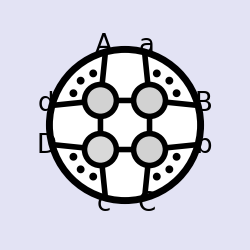
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<loop_amplitudes.m
```

```mathematica
n=9;
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c])};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>(Sort[i] Signature[i])/Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Tota//abfactorl[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
myComplement[x_,y_]:=Select[x,!MemberQ[y,#]&];
```

```mathematica
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
uvtoab[a_,b_,c_,n_]:={u1->(ab[n,1,a-1,a]ab[b-1,b,c-1,c])/(ab[n,1,b-1,b]ab[a-1,a,c-1,c]),v1->(ab[a-1,a,b-1,b]ab[c-1,c,n,1])/(ab[n,1,b-1,b]ab[a-1,a,c-1,c]),un->(ab[a-1,a,b-1,b]ab[c-1,c,n-1,n])/(ab[a-1,a,c-1,c]ab[b-1,b,n-1,n]),vn->(ab[b-1,b,c-1,c]ab[a-1,a,n-1,n])/(ab[a-1,a,c-1,c]ab[b-1,b,n-1,n]),Subscript[τ, u]->-(ab[c-1,c,n-1,n]ab[n,1,2,3])/(ab[n,1,c-1,c]ab[2,3,n-1,n]),Subscript[τ, v]->If[a===2,0,-(ab[a-1,a,n-1,n]ab[n,1,2,3])/(ab[n,1,a-1,a]ab[2,3,n-1,n])],Δ1->If[a===2,1-v1,Sqrt[(1-u1-v1)^2-4u1 v1]],Δn->If[c===n-1,1-vn,Sqrt[(1-un-vn)^2-4un vn]]};
rationalpara1={τ->Subscript[τ, u]((t-v1(1-vn-Δn))(t-v1(1-vn+Δn)))/((t-un(1-u1-Δ1))(t-un(1-u1+Δ1)))};
rationalpara2={τ->Subscript[τ, v]((t-u1(1-un-Δn))(t-u1(1-un+Δn)))/((t-vn(1-v1-Δ1))(t-vn(1-v1+Δ1)))};
```

```mathematica
dabtoeta=dab[x__]:>Apply[ab,Partition[{x},4,1,5],{1}].η/@{x};
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};
repR1={R[cap[{a_,b_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1],R[cap[{b_,a_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1]};
repR2={R[cap[{a___},{c_,n,n+1}],d___,n+1,cap[{n,n+1},m__]]:>(ab[c,d,n+1]ab[a,n,n+1])/(ab[c,a,n+1]ab[d,n,n+1])R[c,cap[{a},{c,n,n+1}],d,n]R[a,c,n,n+1]};
qlogtodabm={Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n])};
preab[exp_]:=neab[exp/(ab@@@Subsets[Range[n+1],{4}])];
numabfactor[exp_]:=ab@@@Subsets[Range[n+1],{4}][[Flatten[Position[exp/(ab@@@Subsets[Range[n+1],{4}])//neab,_Integer]]]];
inumabfactor[exp_]:=ab@@@Subsets[Range[n+1],{4}][[Flatten[Position[(exp/(ab@@@Subsets[Range[n+1],{4}]))^-1//neab,_Integer]]]];
dabsimp[exp_]:=Module[{f1,f2,f3},f1=exp/.dabcapexpand/.dabtoeta//neab//Simplify;
f2=dab@@(Cases[f1,η[_],Infinity]/.η->List//Flatten);
f3=Times@@(exp/f2/.dabcapexpand/.dabtoeta//neab//Simplify//numabfactor);
If[Abs[( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.i_η:>1//neab]<10,f2*f3 ( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.sortall,exp]
];

absim[exp_]:=Module[{f1},f1=Times@@(exp//numabfactor);
If[Abs[exp/f1//neab]<10,f1(exp/f1//neab),exp]
];
```

```mathematica
randomPositiveZs[20];
```

## Rationalizations of the 4-mass box {{a,...,b-1},{b,...,c-1},{c,...,n},{n+1,...,a-1}}

### Example: {{3,4},{5,6},{7,8,9},{10,1,2}} using rational parameterization 1

```mathematica
rationalizebox1[a_,b_,c_,n_]:=
With[{μ=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]]ab[a-1,a,b-1,b]),ν=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[b-1,b,c-1,c])/(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]]ab[a-1,a,b-1,b])},dlog[(t-un v1 (1+(2 ab[-1+a,a,-1+c,n] ab[-1+b,b,-1+c,c])/ab[-1+c,cap1[{-1+a,a},{-1+b,b},{c,n}]]))/(t-un v1 (1+(2 ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,-1+c}]])/(ab[-1+a,a,-1+b,b] ab[-1+n,n,1,-1+c])))] Qlog[ab[-1+n
n,1,cap[{-1+a,a},{-1+b,b,-1+c}]]/ab[-1+n,n,1,-1+c]] R[-1+a,a,-1+b,b,-1+c]+dlog[(t-un v1 (1+(2 ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,c}]])/(ab[-1+a,a,-1+b,b] ab[-1+n,n,1,c])))/(t+un v1+(2 un v1 ab[-1+a,a,-1+c,c] ab[-1+b,b,c,n])/ab[c,cap1[{-1+a,a},{-1+b,b},{-1+c,n}]])] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,c}]]/ab[-1+n,n,1,c]] R[-1+a,a,-1+b,b,c]+dlog[t-(un v1 (μ+ν))/(μ-ν)] Qlog[ab[-1+n,n,1,-1+c]/ab[-1+n,n,1,c]] R[-1+a,a,-1+b,b,cap[{-1+c,c},{-1+n,n,1}]]+dlog[(t+un v1 (-1+(2 ab[-1+a,a,-1+b,n] ab[-1+b,b,-1+c,c])/(ab[-1+a,a,-1+b,b] ab[-1+b,-1+c,c,n])))/(t-un v1 (1+(2 ab[-1+n,n,1,cap[{-1+a,a},{-1+b,-1+c,c}]])/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,a,-1+b}]]))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,-1+c,c}]]/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,a,-1+b}]]] R[-1+a,a,-1+b,-1+c,c]+dlog[(t-un v1 (1+(2 ab[-1+n,n,1,cap[{-1+a,a},{b,-1+c,c}]])/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,a,b}]]))/(t+un v1 (-1+(2 ab[-1+a,a,b,n] ab[-1+b,b,-1+c,c])/(ab[-1+a,a,-1+b,b] ab[b,-1+c,c,n])))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{b,-1+c,c}]]/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,a,b}]]] R[-1+a,a,b,-1+c,c]+dlog[(t+un v1 (1-(2 ab[-1+a,a,-1+c,c] ab[-1+a,-1+b,b,n])/(ab[-1+a,a,-1+b,b] ab[-1+a,-1+c,c,n])))/(t-un v1 (1+(2 ab[-1+b,b,-1+c,c] ab[-1+n,n,1,-1+a])/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,-1+b,b}]]))] Qlog[ab[-1+n,n,1,-1+a]/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,-1+b,b}]]] R[-1+a,-1+b,b,-1+c,c]+dlog[(t-un v1 (1+(2 ab[-1+b,b,-1+c,c] ab[-1+n,n,1,a])/ab[-1+n,n,1,cap[{-1+c,c},{a,-1+b,b}]]))/(t+un v1 (1-(2 ab[-1+a,a,-1+c,c] ab[a,-1+b,b,n])/(ab[-1+a,a,-1+b,b] ab[a,-1+c,c,n])))] Qlog[ab[-1+n,n,1,a]/ab[-1+n,n,1,cap[{-1+c,c},{a,-1+b,b}]]] R[a,-1+b,b,-1+c,c]+dlog[(t-un v1)/(t+un v1-2 un v1 μ)] Qlog[ab[-1+n,n,1,-1+a]/ab[-1+n,n,1,a]] R[cap[{-1+a,a},{-1+n,n,1}],-1+b,b,-1+c,c]];
```

```mathematica
(* Check two box coefficients equal *)
```

```mathematica
radne=RandomInteger[{1,n},2];
radf=RandomInteger[{1,n},3];
origincoe1p=fuse[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef1p=FullSimplify[Limit[Simplify[origincoe1p,τ>0],e->0]/.rationalpara1//.uvtoab[3,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[3,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[3,5,7,9]]];
origincoe1m=fuse[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef1m=FullSimplify[Limit[Simplify[origincoe1m,τ>0],e->0]/.rationalpara1//.uvtoab[3,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[3,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[3,5,7,9]]];
subcoef1=subcoef1p-subcoef1m;
{radf,radne,subcoef1/.t->RandomReal[{neabp[un(1-u1+Δ1)//.uvtoab[3,5,7,9]],neabp[(1-vn+Δn) v1//.uvtoab[3,5,7,9]]}],((fuse[rationalizebox1[3,5,7,9]//.uvtoab[3,5,7,9]/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[radne]/.DmatrixEval3[radf,3]//Simplify)-(ab[2,3,8,9]/ab[1,2,3,9] D[τ/.rationalpara1,t]//.uvtoab[3,5,7,9]//neabp)subcoef1//neab//Simplify}
```

```mathematica
rationalpara2
```

{τ→((t-u1 (1-un-Δn)) (t-u1 (1-un+Δn)) τ_v)/((t-vn (1-v1-Δ1)) (t-vn (1-v1+Δ1)))}

```mathematica
rationalpara1
```

{τ→((t-v1 (1-vn-Δn)) (t-v1 (1-vn+Δn)) τ_u)/((t-un (1-u1-Δ1)) (t-un (1-u1+Δ1)))}

```mathematica
rationalizeintegral1[a_,b_,c_,n_]:=With[{μ=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]]ab[a-1,a,b-1,b]),ν=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[b-1,b,c-1,c])/(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]]ab[a-1,a,b-1,b])},-Li[1-(t-un v1)/(t+un v1)]+Li[1-((t-un v1 (-1+2 μ)) ν)/(μ (t-un v1 (1+2 ν)))]-1/2 log[(1-(t-un v1)/(t+un v1))(1-((t-un v1 (-1+2 μ)) ν)/(μ (t-un v1 (1+2 ν))))] log[((t-un v1)/(t+un v1))/(((t-un v1 (-1+2 μ)) ν)/(μ (t-un v1 (1+2 ν))))]]//.uvtoab[a,b,c,n];
```

```mathematica
(* Check two box integral Equal *)
```

```mathematica
{μ=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]]ab[a-1,a,b-1,b]),ν=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[b-1,b,c-1,c])/(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]]ab[a-1,a,b-1,b])}
```

{(ab[9,cap1[{1,8},{-1+a,a},{-1+b,b}]] ab[-1+a,a,-1+c,c])/(ab[9,cap1[{1,8},{-1+a,a},{-1+c,c}]] ab[-1+a,a,-1+b,b]),(ab[9,cap1[{1,8},{-1+a,a},{-1+b,b}]] ab[-1+b,b,-1+c,c])/(ab[9,cap1[{1,8},{-1+b,b},{-1+c,c}]] ab[-1+a,a,-1+b,b])}

```mathematica
originbox1=(scalarBoxIntegral[{{3,4},{5,6},{7,8,9},{10,1,2}}]//fullabB//neabp)/.{Li[x_]:>PolyLog[2,Simplify[Limit[x,e->0]/.rationalpara1//.uvtoab[3,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[3,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[3,5,7,9]]]],log[x_]:>Log[Simplify[Limit[x,e->0]/.rationalpara1//.uvtoab[3,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[3,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[3,5,7,9]]]]};
rant=RandomReal[{neabp[un (1-u1+Δ1)//.uvtoab[3,5,7,9]],neabp[v1 (1-vn+Δn)//.uvtoab[3,5,7,9]]}];
N[originbox1-((rationalizeintegral1[3,5,7,9]//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant,30]
```

4.17444×10^-14

```mathematica
μ=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]]ab[a-1,a,b-1,b]),ν=(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]]ab[b-1,b,c-1,c])/(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]]ab[a-1,a,b-1,b])
```

### Example: {{3,4},{5,6},{7,8,9},{10,1,2}} using rational parameterization 2

```mathematica
rationalizebox2[a_,b_,c_,n_]:=With[{μ=(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]] ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]] ab[b-1,b,c-1,c]),ν=(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]] ab[a-1,a,b-1,b])/(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]] ab[b-1,b,c-1,c])},dlog[(t-u1 vn (1+(2 ab[1,-1+c,-1+n,n] ab[-1+a,a,-1+b,b])/ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,-1+c}]]))/(t+u1 vn (1-(2 ab[-1+a,a,-1+c,c] ab[-1+b,b,-1+c,n])/(ab[-1+a,a,-1+c,n] ab[-1+b,b,-1+c,c])))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,-1+c}]]/ab[-1+n,n,1,-1+c]] R[-1+a,a,-1+b,b,-1+c]+dlog[(t+u1 vn (1-(2 ab[-1+a,a,-1+c,c] ab[-1+b,b,c,n])/(ab[-1+a,a,c,n] ab[-1+b,b,-1+c,c])))/(t-u1 vn (1+(2 ab[1,c,-1+n,n] ab[-1+a,a,-1+b,b])/ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,c}]]))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,c}]]/ab[-1+n,n,1,c]] R[-1+a,a,-1+b,b,c]+dlog[(t-u1 vn)/(t+u1 vn (1-2 μ))] Qlog[ab[-1+n,n,1,-1+c]/ab[-1+n,n,1,c]] R[-1+a,a,-1+b,b,cap[{-1+c,c},{-1+n,n,1}]]+dlog[(t+u1 vn+(2 u1 vn ab[1,-1+b,-1+n,n] ab[-1+a,a,-1+c,c])/ab[-1+n,n,1,cap[{-1+a,a},{-1+b,-1+c,c}]])/(t+u1 vn (-1+(2 ab[-1+a,a,-1+b,b] ab[-1+b,-1+c,c,n])/(ab[-1+a,a,-1+b,n] ab[-1+b,b,-1+c,c])))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,-1+c,c}]]/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,a,-1+b}]]] R[-1+a,a,-1+b,-1+c,c]+dlog[(t+u1 vn (-1+(2 ab[-1+a,a,-1+b,b] ab[b,-1+c,c,n])/(ab[-1+a,a,b,n] ab[-1+b,b,-1+c,c])))/(t+u1 vn+(2 u1 vn ab[1,b,-1+n,n] ab[-1+a,a,-1+c,c])/ab[-1+n,n,1,cap[{-1+a,a},{b,-1+c,c}]])] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{b,-1+c,c}]]/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,a,b}]]] R[-1+a,a,b,-1+c,c]+dlog[(t-u1 vn (1+(2 ab[-1+n,n,1,cap[{-1+c,c},{-1+a,-1+b,b}]])/(ab[1,-1+a,-1+n,n] ab[-1+b,b,-1+c,c])))/(t-u1 vn+(2 u1 vn ab[-1+a,a,-1+b,b] ab[-1+a,-1+c,c,n])/ab[-1+a,cap1[{-1+b,b},{-1+c,c},{a,n}]])] Qlog[ab[-1+n,n,1,-1+a]/ab[-1+n,n,1,cap[{-1+c,c},{-1+a,-1+b,b}]]] R[-1+a,-1+b,b,-1+c,c]+dlog[(t+u1 vn-(2 u1 vn ab[-1+a,a,-1+c,c] ab[a,-1+b,b,n])/ab[a,cap1[{-1+b,b},{-1+c,c},{-1+a,n}]])/(t-u1 vn (1+(2 ab[-1+n,n,1,cap[{-1+c,c},{a,-1+b,b}]])/(ab[1,a,-1+n,n] ab[-1+b,b,-1+c,c])))] Qlog[ab[-1+n,n,1,a]/ab[-1+n,n,1,cap[{-1+c,c},{a,-1+b,b}]]] R[a,-1+b,b,-1+c,c]+dlog[t-(u1 vn (μ+ν))/(μ-ν)] Qlog[ab[-1+n,n,1,-1+a]/ab[-1+n,n,1,a]] R[-1+c,c,-1+b,b,cap[{-1+a,a},{-1+n,n,1}]]];
```

```mathematica
(* Check two box coefficients equal *)
```

```mathematica
radne=RandomInteger[{1,n},2];
radf=RandomInteger[{1,n},3];
origincoe2p=fuse[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef2p=Simplify[Limit[Simplify[origincoe2p,τ>0],e->0]/.rationalpara2//.uvtoab[3,5,7,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[3,5,7,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[3,5,7,9]]];
origincoe2m=fuse[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef2m=Simplify[Limit[Simplify[origincoe2m,τ>0],e->0]/.rationalpara2//.uvtoab[3,5,7,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[3,5,7,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[3,5,7,9]]];
subcoef2=subcoef2p-subcoef2m;{radf,radne,subcoef2/.t->RandomReal[{neabp[u1 (1-un+Δn)//.uvtoab[3,5,7,9]],neabp[(1-v1+Δ1) vn//.uvtoab[3,5,7,9]]}],((fuse[rationalizebox2[3,5,7,9]//.uvtoab[3,5,7,9]/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[radne]/.DmatrixEval3[radf,3]//Simplify)-(ab[2,3,8,9]/ab[1,2,3,9] D[τ/.rationalpara2,t]//.uvtoab[3,5,7,9]//neabp)subcoef2//Simplify}
```

{{5,2,3},{1,6},3.74063×10^-7,0}

```mathematica
subcoef2
```

(772007936 (351430265354989977428688-6238673514958501373639848002 t+95838092604399038124974952169 t^2)^2 (966699506907980066510905536-18175526639474967514951428140784 t+297768953721867811454297176389083 t^2))/(11305089 (-1193821214686528392+10091022209094416315521 t) (-9178002648121551936282174528+199619628836664492390184800825168 t+10539027529427949025489120565168423 t^2) (137767656394514583219847450356288-557642085045030243333895734372720528 t+4912126911559961556164027845797482347337 t^2))-(4480102090302007672832 (351430265354989977428688-6238673514958501373639848002 t+95838092604399038124974952169 t^2)^2 (15536989715192693657004760832723904-277892433878957672803964188403096656368 t+38873638632847029178639634770154658135823 t^2))/(405 (34658123560776+99993461602868551 t) (-900650855477422749672+15867207385371202000956301 t) (137767656394514583219847450356288-557642085045030243333895734372720528 t+4912126911559961556164027845797482347337 t^2) (459884781169639096250911264361577792-8117061307006164390257176153879311875472 t+3391616755106636656071119889237040603226941 t^2))

```mathematica
(* Check two box integrals equal *)
```

```mathematica
rationalizeintegral2[a_,b_,c_,n_]:=With[{μ=(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]] ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]] ab[b-1,b,c-1,c]),ν=(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]] ab[a-1,a,b-1,b])/(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]] ab[b-1,b,c-1,c])},Li[(t-u1 vn)/(t+u1 vn)]-Li[((t-u1 vn (-1+2 μ)) ν)/(μ (t-u1 vn (1+2 ν)))]+1/2 log[((t-u1 vn) (t-u1 vn (-1+2 μ)) ν)/((t+u1 vn) μ (t-u1 vn (1+2 ν)))] log[(1-(t-u1 vn)/(t+u1 vn))/(1-((t-u1 vn (-1+2 μ)) ν)/(μ (t-u1 vn (1+2 ν))))]]//.uvtoab[a,b,c,n];
```

```mathematica
originbox2=(scalarBoxIntegral[{{3,4},{5,6},{7,8,9},{10,1,2}}]//fullabB//neabp)/.{Li[x_]:>PolyLog[2,Simplify[Limit[x,e->0]/.rationalpara2//.uvtoab[3,5,7,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[3,5,7,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[3,5,7,9]]]],log[x_]:>Log[Simplify[Limit[x,e->0]/.rationalpara2//.uvtoab[3,5,7,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[3,5,7,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[3,5,7,9]]]]};
rant=RandomReal[{neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[3,5,7,9]],neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[3,5,7,9]]}];
N[originbox2-((rationalizeintegral2[3,5,7,9]//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant,30]
```

1.5099×10^-14

## Rationalizations of the 4-mass box {{2,...,b-1},{b,...,c-1},{c,...,n},{n+1,1}}

For this case, since τ_v= ∞, we  use rationalize parameterization 1

```mathematica
rationalpara1
```

{τ→((t-v1 (1-vn-Δn)) (t-v1 (1-vn+Δn)) τ_u)/((t-un (1-u1-Δ1)) (t-un (1-u1+Δ1)))}

```mathematica
uvtoab[2,5,7,9]
```

{u1→0,v1→(ab[1,2,4,5] ab[6,7,9,1])/(ab[1,2,6,7] ab[9,1,4,5]),un→(ab[1,2,4,5] ab[6,7,8,9])/(ab[1,2,6,7] ab[4,5,8,9]),vn→(ab[1,2,8,9] ab[4,5,6,7])/(ab[1,2,6,7] ab[4,5,8,9]),τ_u→-(ab[6,7,8,9] ab[9,1,2,3])/(ab[2,3,8,9] ab[9,1,6,7]),τ_v→0,Δ1→1-v1,Δn→√((1-un-vn)^2-4 un vn)}

```mathematica
rerationalizebox1[b_,c_,n_]:=
With[{μ=(ab[n,cap1[{1,n-1},{1,2},{b-1,b}]]ab[1,2,c-1,c])/(ab[n,cap1[{1,n-1},{1,2},{c-1,c}]]ab[1,2,b-1,b]),ν=(ab[n,cap1[{1,n-1},{1,2},{b-1,b}]]ab[b-1,b,c-1,c])/(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]]ab[1,2,b-1,b])},dlog[(t-un v1 (1+(2 ab[1,2,-1+c,n] ab[-1+b,b,-1+c,c])/ab[-1+c,cap1[{1,2},{-1+b,b},{c,n}]]))/((t-(un v1 (μ+ν))/(μ-ν)) (t-un v1 (1-(2 ab[1,2,-1+n,n] ab[1,-1+b,b,-1+c])/(ab[1,2,-1+b,b] ab[1,-1+c,-1+n,n]))))] Qlog[ab[-1+n,n,1,2]/ab[-1+n,n,1,-1+c]] R[1,2,-1+b,b,-1+c]+dlog[((t-(un v1 (μ+ν))/(μ-ν)) (t-un v1 (1-(2 ab[1,2,-1+n,n] ab[1,-1+b,b,c])/(ab[1,2,-1+b,b] ab[1,c,-1+n,n]))))/(t+un v1+(2 un v1 ab[1,2,-1+c,c] ab[-1+b,b,c,n])/ab[c,cap1[{1,2},{-1+b,b},{-1+c,n}]])] Qlog[ab[-1+n,n,1,2]/ab[-1+n,n,1,c]] R[1,2,-1+b,b,c]+dlog[(t+un v1 (-1+(2 ab[1,2,-1+b,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+b,b] ab[-1+b,-1+c,c,n])))/((t-(un v1 (μ+ν))/(μ-ν)) (t-un v1 (1-(2 ab[1,2,-1+n,n] ab[1,-1+b,-1+c,c])/ab[-1+n,n,1,cap[{-1+c,c},{1,2,-1+b}]])))] Qlog[ab[-1+n,n,1,2]/ab[-1+n,n,1,cap[{-1+c,c},{1,2,-1+b}]]] R[1,2,-1+b,-1+c,c]+dlog[((t-(un v1 (μ+ν))/(μ-ν)) (t-un v1 (1-(2 ab[1,2,-1+n,n] ab[1,b,-1+c,c])/ab[-1+n,n,1,cap[{-1+c,c},{1,2,b}]])))/(t+un v1 (-1+(2 ab[1,2,b,n] ab[-1+b,b,-1+c,c])/(ab[1,2,-1+b,b] ab[b,-1+c,c,n])))] Qlog[ab[-1+n,n,1,2]/ab[-1+n,n,1,cap[{-1+c,c},{1,2,b}]]] R[1,2,b,-1+c,c]+dlog[(t+un v1 (1-(2 ab[1,2,-1+c,c] ab[1,-1+b,b,n])/(ab[1,2,-1+b,b] ab[1,-1+c,c,n])))/((t-un v1) (t-(un v1 (μ+ν))/(μ-ν)))] Qlog[ab[-1+n,n,1,2]/ab[-1+n,n,1,cap[{-1+c,c},{1,-1+b,b}]]] R[1,-1+b,b,-1+c,c]+dlog[((t-(un v1 (μ+ν))/(μ-ν)) (t-un v1 (1+(2 ab[-1+b,b,-1+c,c] ab[-1+n,n,1,2])/ab[-1+n,n,1,cap[{-1+c,c},{2,-1+b,b}]])))/(t+un v1 (1-(2 ab[1,2,-1+c,c] ab[2,-1+b,b,n])/(ab[1,2,-1+b,b] ab[2,-1+c,c,n])))] Qlog[ab[-1+n,n,1,2]/ab[-1+n,n,1,cap[{-1+c,c},{2,-1+b,b}]]] R[2,-1+b,b,-1+c,c]];
```

### Example: {{2,3,4},{5,6},{7,8,9},{10,1}} using rational parameterization 1

```mathematica
{1,2,4,5,6,7,8,9}[[{1,1}]]
```

{1,1}

```mathematica
radne={1,2,4,5,6,7,8,9}[[RandomInteger[{1,n-1},2]]];
radf={1,2,4,5,6,7,8,9}[[RandomInteger[{1,n-1},3]]];
origincoe1p=fuse[Total[rForm[onShellGraph[2][{{2,3,4},{5,6},{7,8,9},{10,1}},{0,0,0,0}]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef1p=FullSimplify[Limit[Simplify[origincoe1p,τ>0],e->0]/.rationalpara1//.uvtoab[2,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[2,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[2,5,7,9]]];
origincoe1m=fuse[Total[rForm[onShellGraph[2][{{2,3,4},{5,6},{7,8,9},{10,1}},{0,0,0,0}]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef1m=FullSimplify[Limit[Simplify[origincoe1m,τ>0],e->0]/.rationalpara1//.uvtoab[2,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[2,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[2,5,7,9]]];
subcoef1=subcoef1p-subcoef1m;
{radf,radne,subcoef1/.t->RandomReal[{neabp[un(1-u1+Δ1)//.uvtoab[2,5,7,9]],neabp[(1-vn+Δn) v1//.uvtoab[2,5,7,9]]}],((fuse[rerationalizebox1[5,7,9]//.uvtoab[2,5,7,9]/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[radne]/.DmatrixEval3[radf,3]//Simplify)-(ab[2,3,8,9]/ab[1,2,3,9] D[τ/.rationalpara1,t]//.uvtoab[2,5,7,9]//neabp)subcoef1//neab//Simplify}
```

{{7,8,4},{8,1},0,0}

```mathematica
(*Check two box integrals equal*)
```

```mathematica
originbox1=(scalarBoxIntegral[{{2,3,4},{5,6},{7,8,9},{10,1}}]//fullabB//neabp)/.{Li[x_]:>PolyLog[2,Simplify[Limit[x,e->0]/.rationalpara1//.uvtoab[2,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[2,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[2,5,7,9]]]],log[x_]:>Log[Simplify[Limit[x,e->0]/.rationalpara1//.uvtoab[2,5,7,9]//neabp,neabp[un (1-u1+Δ1)//.uvtoab[2,5,7,9]]<t<neabp[v1 (1-vn+Δn)//.uvtoab[2,5,7,9]]]]};
rant=RandomReal[{neabp[un (1-u1+Δ1)//.uvtoab[2,5,7,9]],neabp[v1 (1-vn+Δn)//.uvtoab[2,5,7,9]]}];
N[originbox1-((rationalizeintegral1[2,5,7,9]//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant,30]
```

-4.44089×10^-16

## Rationalizations of the 4-mass box {{a,...,b-1},{b,...,n-2},{n-1,n},{n+1,...,a-1}}

For this case, since τ_u=0, we  use rationalize parameterization 2

```mathematica
rationalpara2
```

{τ→((t-u1 (1-un-Δn)) (t-u1 (1-un+Δn)) τ_v)/((t-vn (1-v1-Δ1)) (t-vn (1-v1+Δ1)))}

```mathematica
uvtoab[4,6,8,9]
```

{u1→(ab[5,6,7,8] ab[9,1,3,4])/(ab[3,4,7,8] ab[9,1,5,6]),v1→(ab[3,4,5,6] ab[7,8,9,1])/(ab[3,4,7,8] ab[9,1,5,6]),un→0,vn→(ab[3,4,8,9] ab[5,6,7,8])/(ab[3,4,7,8] ab[5,6,8,9]),τ_u→0,τ_v→-(ab[3,4,8,9] ab[9,1,2,3])/(ab[2,3,8,9] ab[9,1,3,4]),Δ1→√((1-u1-v1)^2-4 u1 v1),Δn→1-vn}

### Example: {{4,5},{6,7},{8,9},{10,1,2,3}} using rational parameterization 2

```mathematica
rationalpara2[4,6,8,9]
```

{τ→((t-u1 (1-un-Δn)) (t-u1 (1-un+Δn)) τ_v)/((t-vn (1-v1-Δ1)) (t-vn (1-v1+Δ1)))}[4,6,8,9]

```mathematica
rerationalizebox2[a_,b_,n_]:=With[{μ=(ab[n,cap1[{1,-1+n},{-1+b,b},{-2+n,-1+n}]] ab[-1+a,a,-2+n,-1+n])/(ab[n,cap1[{1,-1+n},{-1+a,a},{-2+n,-1+n}]] ab[-1+b,b,-2+n,-1+n]),ν=(ab[n,cap1[{1,-1+n},{-1+b,b},{-2+n,-1+n}]] ab[-1+a,a,-1+b,b])/(ab[n,cap1[{1,-1+n},{-1+a,a},{-1+b,b}]] ab[-1+b,b,-2+n,-1+n])},dlog[((t-(u1 vn (μ+ν))/(μ-ν)) (t-u1 vn (1+(2 ab[1,-2+n,-1+n,n] ab[-1+a,a,-1+b,b])/ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,-2+n}]])))/(t+u1 vn (1-(2 ab[-1+a,a,-2+n,-1+n] ab[-1+b,b,-2+n,n])/(ab[-1+a,a,-2+n,n] ab[-1+b,b,-2+n,-1+n])))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,-2+n}]]/ab[-1+n,n,1,-2+n]] R[-1+a,a,-1+b,b,-2+n]+dlog[(t-u1 (1-un+Δn))/((t-u1 vn) (t-(u1 vn (μ+ν))/(μ-ν)))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,b,-1+n}]]/ab[-1+n,n,1,-2+n]] R[-1+a,a,-1+b,b,-1+n]+dlog[((t-(u1 vn (μ+ν))/(μ-ν)) (t-u1 vn (1-(2 ab[1,-2+n,-1+n,n] ab[-1+a,a,-1+b,-1+n])/ab[-1+n,n,1,cap[{-1+a,a},{-1+b,-2+n,-1+n}]])))/(t+u1 vn (-1+(2 ab[-1+a,a,-1+b,b] ab[-1+b,-2+n,-1+n,n])/(ab[-1+a,a,-1+b,n] ab[-1+b,b,-2+n,-1+n])))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{-1+b,-2+n,-1+n}]]/ab[-1+n,n,1,-2+n]] R[-1+a,a,-1+b,-2+n,-1+n]+dlog[(t+u1 vn (-1+(2 ab[-1+a,a,-1+b,b] ab[b,-2+n,-1+n,n])/(ab[-1+a,a,b,n] ab[-1+b,b,-2+n,-1+n])))/((t-(u1 vn (μ+ν))/(μ-ν)) (t-u1 vn (1-(2 ab[1,-2+n,-1+n,n] ab[-1+a,a,b,-1+n])/ab[-1+n,n,1,cap[{-1+a,a},{b,-2+n,-1+n}]])))] Qlog[ab[-1+n,n,1,cap[{-1+a,a},{b,-2+n,-1+n}]]/ab[-1+n,n,1,-2+n]] R[-1+a,a,b,-2+n,-1+n]+dlog[((t-(u1 vn (μ+ν))/(μ-ν)) (t-u1 vn (1-(2 ab[1,-2+n,-1+n,n] ab[-1+a,-1+b,b,-1+n])/(ab[1,-1+a,-1+n,n] ab[-1+b,b,-2+n,-1+n]))))/(t-u1 vn+(2 u1 vn ab[-1+a,a,-1+b,b] ab[-1+a,-2+n,-1+n,n])/ab[-1+a,cap1[{-1+b,b},{-2+n,-1+n},{a,n}]])] Qlog[ab[-1+n,n,1,-1+a]/ab[-1+n,n,1,-2+n]] R[-1+a,-1+b,b,-2+n,-1+n]+dlog[(t+u1 vn (1-(2 ab[-1+a,a,-2+n,-1+n] ab[a,-1+b,b,n])/ab[a,cap1[{-1+b,b},{-2+n,-1+n},{-1+a,n}]]))/((t-(u1 vn (μ+ν))/(μ-ν)) (t-u1 vn (1-(2 ab[1,-2+n,-1+n,n] ab[a,-1+b,b,-1+n])/(ab[1,a,-1+n,n] ab[-1+b,b,-2+n,-1+n]))))] Qlog[ab[-1+n,n,1,a]/ab[-1+n,n,1,-2+n]] R[a,-1+b,b,-2+n,-1+n]];
```

```mathematica
radne=RandomInteger[{3,n},2];
radf=RandomInteger[{3,n-1},3];
origincoe2p=fuse[Total[rForm[onShellGraph[2][{{4,5},{6,7},{8,9},{10,1,2,3}},{0,0,0,0}]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef2p=Simplify[Limit[Simplify[origincoe2p,τ>0],e->0]/.rationalpara2//.uvtoab[4,6,8,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[4,6,8,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[4,6,8,9]]];
origincoe2m=fuse[Total[rForm[onShellGraph[2][{{4,5},{6,7},{8,9},{10,1,2,3}},{0,0,0,0}]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef2m=Simplify[Limit[Simplify[origincoe2m,τ>0],e->0]/.rationalpara2//.uvtoab[4,6,8,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[4,6,8,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[4,6,8,9]]];
subcoef2=subcoef2p-subcoef2m;{radf,radne,subcoef2/.t->RandomReal[{neabp[u1 (1-un+Δn)//.uvtoab[4,6,8,9]],neabp[(1-v1+Δ1) vn//.uvtoab[4,6,8,9]]}],((fuse[rerationalizebox2[4,6,9]//.uvtoab[4,6,8,9]/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[radne]/.DmatrixEval3[radf,3]//Simplify)-(ab[2,3,8,9]/ab[1,2,3,9] D[τ/.rationalpara2,t]//.uvtoab[4,6,8,9]//neabp)subcoef2//Simplify}
```

{{5,3,8},{9,4},-0.0000210401,0}

```mathematica
rationalizeintegral2[a_,b_,c_,n_]:=With[{μ=(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]] ab[a-1,a,c-1,c])/(ab[n,cap1[{1,n-1},{a-1,a},{c-1,c}]] ab[b-1,b,c-1,c]),ν=(ab[n,cap1[{1,n-1},{b-1,b},{c-1,c}]] ab[a-1,a,b-1,b])/(ab[n,cap1[{1,n-1},{a-1,a},{b-1,b}]] ab[b-1,b,c-1,c])},Li[(t-u1 vn)/(t+u1 vn)]-Li[((t-u1 vn (-1+2 μ)) ν)/(μ (t-u1 vn (1+2 ν)))]+1/2 log[((t-u1 vn) (t-u1 vn (-1+2 μ)) ν)/((t+u1 vn) μ (t-u1 vn (1+2 ν)))] log[(1-(t-u1 vn)/(t+u1 vn))/(1-((t-u1 vn (-1+2 μ)) ν)/(μ (t-u1 vn (1+2 ν))))]]//.uvtoab[a,b,c,n];
```

```mathematica
originbox2=(scalarBoxIntegral[{{4,5},{6,7},{8,9},{10,1,2,3}}]//fullabB//neabp)/.{Li[x_]:>PolyLog[2,Simplify[Limit[x,e->0]/.rationalpara2//.uvtoab[4,6,8,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[4,6,8,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[4,6,8,9]]]],log[x_]:>Log[Simplify[Limit[x,e->0]/.rationalpara2//.uvtoab[4,6,8,9]//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[4,6,8,9]]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[4,6,8,9]]]]};
rant=RandomReal[{neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))//.uvtoab[4,6,8,9]],neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn//.uvtoab[4,6,8,9]]}];
N[originbox2-((rationalizeintegral2[4,6,8,9]//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant,30]
```

2.22045×10^-16

## Rationalizations of the 4-mass box {{2,...,b-1},{b,...,n-2},{n-1,n},{n+1,1}}

```mathematica
tautot[b_,n_]:={τ->-((ab[1,2,3,n]ab[n-1,cap1[{1,2},{b-1,b},{n,n-2}]])/(ab[2,3,n-1,n]ab[1,cap1[{b-1,b},{n-2,n-1},{2,n}]]))(t+(ab[1,2,n-2,n-1]ab[1,b-1,b,n-1]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[n-1,cap1[{1,2},{b-1,b},{n,n-2}]]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))/(t(t+1))};
```

```mathematica
Cases[rForm[onShellGraph[2][{{2,3,4,5},{6,7},{8,9},{10,1}},{0,0,0,0}]],Sqrt[_],Infinity]//Union
```

{√(-(4 ab[1,2,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,1,2])/(ab[1,2,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[1,2,5,6] ab[7,8,9,10])/(ab[1,2,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,1,2])/(ab[1,2,7,8] ab[5,6,9,10]))^2)}

```mathematica
randomPositiveZs[20]
```

```mathematica
Limit[-(4 ab[1,2,5,6] ab[5,6,7,8] ab[7,8,9,10] ab[9,10,1,2])/(ab[1,2,7,8]^2 ab[5,6,9,10]^2)+(1-(ab[1,2,5,6] ab[7,8,9,10])/(ab[1,2,7,8] ab[5,6,9,10])-(ab[5,6,7,8] ab[9,10,1,2])/(ab[1,2,7,8] ab[5,6,9,10]))^2//fullabB//neabp,e->0]/.tautot[6,9]//neabp//Simplify
```

```mathematica
tautot[6,9]//neabp
```

{τ→(92443643712 (9481950337024/9600904688743+t))/(3970381730743 t (1+t))}

```mathematica
randomPositiveZs[20];
```

```mathematica
τ/.tautot[5,9]//neabp
```

```mathematica
rationalbox[b_,n_]:=Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,n-2]](dlog[(t+(ab[1,2,n-2,n]ab[1,b-1,b,n-1])/ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]])/(t+(ab[1,2,n-2,n-1]ab[1,b-1,b,n-2]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[n-2,cap1[{1,2},{b-1,b},{n-1,n}]]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))]R[1,2,b-1,b,n-2]+dlog[(t+(ab[1,2,n-2,n-1]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[2,n-2,n-1,n]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))/(t+(ab[1,b-1,b,n-1]ab[2,cap1[{b-1,b},{n-2,n-1},{1,n}]])/(ab[2,b-1,b,n-1]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))]R[2,b-1,b,n-2,n-1]
+dlog[(t+(ab[1,2,b-1,n]ab[1,2,n-2,n-1]ab[1,b,b-1,n-1])/(ab[1,2,b-1,n-1]ab[1,cap1[{b,b-1},{n-2,n-1},{n,2}]]))/(t+(ab[1,b-1,n-2,n-1]ab[n,cap1[{1,2},{b,b-1},{n-2,n-1}]])/(ab[b-1,n-2,n-1,n]ab[1,cap1[{b,b-1},{n-2,n-1},{n,2}]]))]R[1,2,b-1,n-2,n-1]
-dlog[(t+(ab[1,2,b,n]ab[1,2,n-2,n-1]ab[1,b,b-1,n-1])/(ab[1,2,b,n-1]ab[1,cap1[{b,b-1},{n-2,n-1},{n,2}]]))/(t+(ab[1,b,n-2,n-1]ab[n,cap1[{1,2},{b,b-1},{n-2,n-1}]])/(ab[b,n-2,n-1,n]ab[1,cap1[{b,b-1},{n-2,n-1},{n,2}]]))]R[1,2,b,n-2,n-1]+dlog[t+(ab[1,2,n-2,n-1]ab[1,b-1,b,n-1]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[n-1,cap1[{1,2},{b-1,b},{n,n-2}]]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]])]R[1,2,b-1,b,n-1]
+dlog[(t+1)/t]R[1,b-1,b,n-2,n-1]);
```

```mathematica
radne=RandomChoice[{1,2,7,8,9},2];
radf=RandomChoice[{1,2,7,8,9,4,5},3];
origincoep=fuse[Total[rForm[onShellGraph[2][{{2,3,4},{5,6,7},{8,9},{10,1}},{0,0,0,0}]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoefp=Simplify[Limit[Simplify[origincoep,τ>0],e->0]/.tautot[5,9]//neabp,t>0];
origincoem=fuse[Total[rForm[onShellGraph[2][{{2,3,4},{5,6,7},{8,9},{10,1}},{0,0,0,0}]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoefm=Simplify[Limit[Simplify[origincoem,τ>0],e->0]/.tautot[5,9]//neabp,t>0];
subcoef=subcoefp-subcoefm;{radf,radne,subcoef/.t->RandomReal[{0,1}]/(1-RandomReal[{0,1}]),((fuse[rationalbox[5,9]/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[radne]/.DmatrixEval3[radf,3]//Simplify)+(ab[2,3,8,9]/ab[1,2,3,9] D[τ/.tautot[5,9],t]//neabp)subcoef//Simplify}
```

{{2,7,7},{1,7},-0.0424729,0}

```mathematica
originbox=(scalarBoxIntegral[{{2,3,4,5},{6,7},{8,9},{10,1}}]//fullabB//neabp)/.{Li[x_]:>PolyLog[2,Simplify[Limit[x,e->0]/.tautot[6,9]//neabp,t>0]],log[x_]:>Log[Simplify[Limit[x,e->0]/.tautot[6,9]//neabp//neabp,t>0]]};
rant=RandomInteger[10^3]/100;
N[originbox+((rationalintegral[6,9]//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant]
```

4.44089×10^-16

```mathematica
rationalintegral[b_,n_]:=-Li[(t+1)/(t+(ab[1,2,n-2,n-1]ab[1,b-1,b,n])/ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]])]+Li[((ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])t)/(t+(ab[1,b-1,b,n-1]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[b-1,b,n-1,n]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))]-1/2 log[((ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])t)/(t+(ab[1,b-1,b,n-1]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[b-1,b,n-1,n]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))(t+1)/(t+(ab[1,2,n-2,n-1]ab[1,b-1,b,n])/ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]])]log[(1-(t+1)/(t+(ab[1,2,n-2,n-1]ab[1,b-1,b,n])/ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]]))/(1-((ab[1,2,n-1,n]ab[b-1,b,n-2,n-1])/(ab[1,2,n-2,n-1]ab[b-1,b,n-1,n])t)/(t+(ab[1,b-1,b,n-1]ab[n,cap1[{1,2},{b-1,b},{n-2,n-1}]])/(ab[b-1,b,n-1,n]ab[1,cap1[{b-1,b},{n-2,n-1},{n,2}]])))];
```

```mathematica
((rationalintegral[6,9]//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant
```

-6.42781